3.7441-0.0632444 Log[x]+0.00510717 Log[x]^2-0.000137662 Log[x]^3

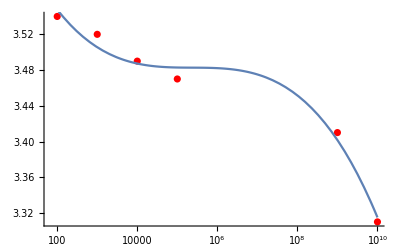

```mathematica
(*dielectric constant versus f*)
data={{10^2,3.54},{10^3,3.52},{10^4,3.49},{10^5,3.47},{10^9,3.41},{10^10,3.31}};
fit=Fit[data,{Log10[x]^3,Log10[x]^2,Log10[x],1},x]
Show[ListLogLinearPlot[data, PlotStyle->Red], LogLinearPlot[3.7440986998901074-0.06324444253194807Log[f]+0.005107166865635606 Log[f]^2-0.000137662448172712 Log[f]^3, {f, 10^2, 10^10}]]
```

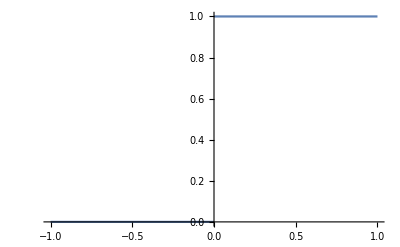

$Aborted

```mathematica
(*Coupled microsttrip line dispersion*)
ClearAll["Global`*"]
μ0=1.257*10^-6;(*free space permeability H/m*)
clight=3*10^8;(*speed of light*)
Z0=50;
μ=31.92*10^-9 ;(*H/in*)
t=0.7*10^-3;(*thckness of the strip in inch*)
H=0.002;(*substrate thickness in inch*)
w=0.0048;(*trace width in inch*)
we=w+t/π(1+Log[2 H/t]) ;(*effective strip widith considering the thickness of the stirp*)
σ=5.96*10^7;(*conductivity of the microstrip material*)
fp=Z0/(2μ H);
ϵs=3.3;
ϵe0=((ϵs+1)/2+(ϵs-1)/2(√(w/(w+12H))));
G=0.6+0.009Z0;
ϵfit[f_]:=3.7440986998901074-0.06324444253194807Log[f]+0.005107166865635606 Log[f]^2-0.000137662448172712 Log[f]^3; (*fit result for dielectric constant dispersion*)
ϵe[f_]:=Piecewise[{{ϵfit[100],f<=10^2},{ϵfit[f],10^2<f<10^10},{ϵfit[10^10],f>10^10}}];
Weff[f_]:=w+((377 H)/(Z0 √ϵe0)-w)/(1+(f^2/fp^2));
Z[f_]:=(377 H)/(Weff[f]*√ϵe[f]);
Rs[f_]:=√(π f μ0/σ);
P=1-(we/(4H))^2;
Q=1+H/we+H/(π we)(Log[(2H)/t]-t/H);
αc[f_]:=(8.68 Rs[f])/(Z0 H)*Q*(we/H+2/π Log[2π ⅇ(we/(2H)+0.94)])^-2(we/H+(we/(π H))/(we/(2H)+0.94));(*conductor loss for w/H>2 dB/cm*)
Plot[HeavisideTheta[τ],{τ,-1,1}]
tanδ[f_]=Piecewise[{{0.008,f<=10^7},{0.008/10^7*f,f>10^7}}];(*loss tangent of the substrate*)

αd[f_]:=27.3 ϵs/(√ϵe[f])(ϵe[f]-1)/(ϵs-1)tanδ[f]/(clight/f);(*dielectric loss dB/cm*)
sdep[f_]:=1/(√(π μ0 σ f));
l = 1;(*cable length in meter*)
L[wid_]=0.00508*10^-6*39.4*l(Log[(2*39.4l)/(wid+H)]+0.5+0.2235(wid+H)/(39.4l));(*total inductance of a microstrip line H*)
Ls[wid_,f_]=Abs[L'[wid]]*sdep[f]/2;
αL[f_]:=(π f)/clight Ls[w,f]/L[w](*Nepers/m*);
list={};
For[t=3*10^-9,t<10*10^-9,t=t+10^-12,list=Append[list,{t*10^9,1/2+√(2/π)NIntegrate[(FourierSinTransform[(HeavisideTheta[τ]-1/2),τ,ω]*ⅇ^(-((αc[ω/(2π)]+αd[ω/(2π)])/8.68*l/100+αL[ω/(2π)]*l))Sin[ω*(t-l/(clight/(√ϵe[ω/(2π)]*(1+Ls[w,ω/(2π)]/(2 L[w])))))]),{ω,0,10^12},MinRecursion->3,MaxRecursion->50]}]];
l = 3;(*cable length in meter*)
L[wid_]=0.00508*10^-6*39.4*l(Log[(2*39.4l)/(wid+H)]+0.5+0.2235(wid+H)/(39.4l));(*total inductance of a microstrip line H*)
Ls[wid_,f_]=Abs[L'[wid]]*sdep[f]/2;
αL[f_]:=(π f)/clight Ls[w,f]/L[w](*Nepers/m*);
For[t=15*10^-9,t<22*10^-9,t=t+10^-12,list=Append[list,{t*10^9,1/2+√(2/π)NIntegrate[(FourierSinTransform[(HeavisideTheta[τ]-1/2),τ,ω]*ⅇ^(-((αc[ω/(2π)]+αd[ω/(2π)])/8.68*l/100+αL[ω/(2π)]*l))Sin[ω*(t-l/(clight/(√ϵe[ω/(2π)]*(1+Ls[w,ω/(2π)]/(2 L[w])))))]),{ω,0,10^12},MinRecursion->3,MaxRecursion->50]}]];
ListPlot[list]
```

```mathematica
Ls[w,f]/L[w];
ϵfit[10^10];
list;
```